```mathematica
ClearAll["Global`*"]
```

```mathematica
x1=-1;
x2=1;
```

```mathematica
Fun[x_]:=0.5*x^4+6*x^2+4
exact=Integrate[Fun[x],{x,x1,x2}]
Integrate[Fun[x],x]
```

12.2

4 x+2 x^3+0.1 x^5

```mathematica
NIntegrate
```

NIntegrate

```mathematica
X[ξ_]:=1/2(1-ξ)*(x1)+1/2(1+ξ)*(x2)
J=D[X[ξ],ξ]
```

1

```mathematica
jac=J;
Q1[]:=Module[{},
xp={0};
wp={2};
Return[{xp,wp}];
];
Q2[]:=Module[{},
xp={-1/√3,1/√3};
wp={1,1};
Return[{xp,wp}];
];
Q3[]:=Module[{},
xp={-√(3/5),0,√(3/5)};
wp={5/9,8/9,5/9};
Return[{xp,wp}];
];
```

```mathematica
{xp,wp}=Q3[]
integral=N[Sum[Fun[xp[[i]]]*wp[[i]]*jac,{i,Length[xp]}]]
```

{{-√(3/5),0,√(3/5)},{5/9,8/9,5/9}}

12.2

```mathematica
Fun[xp]
```

{7.78,4.,7.78}

```mathematica
exact
```

12.2

```mathematica
error=N[FullSimplify[(exact-integral)/exact]]*100
```

100 (1.-1. )

```mathematica
(exact-integral)/exact
```

0.00728597

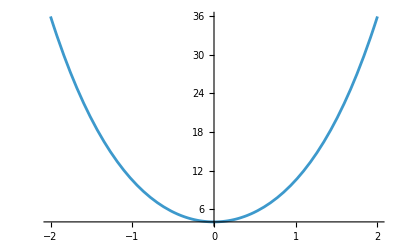

```mathematica
Plot[Fun[x],{x,-2,2}]
```

```mathematica
Fun[0]
```

4.